42

(-2146.92
184.439)

{115191.,0.859577}

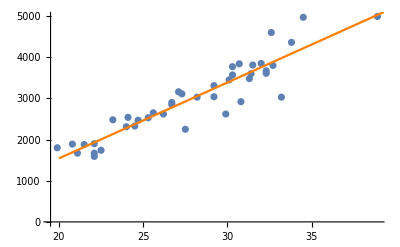

(-2819.04 | -1474.8
160.617 | 208.261)

{15.6478,2.02108}

{-342.49,-2106.96}

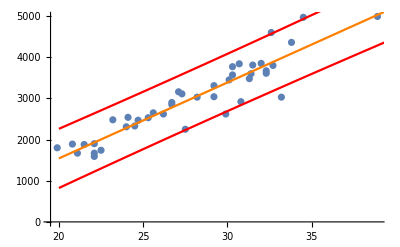

{-669.915,-1779.54}

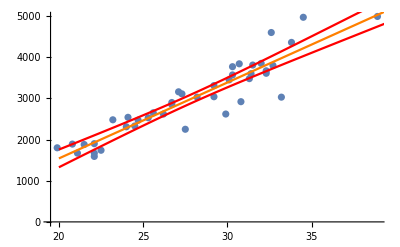

```mathematica
(*x,y*)
rowdata:= {{29.2,30.7,24.7,32.3,31.3,31.5,24.5,19.9,27.3,27.1,24.0,33.8,21.5,32.3,22.5,27.5,25.6,34.5,26.2,26.7,21.1,24.1,32.7,32.6,22.1,25.3,30.8,38.9,22.1,29.2,30.1,31.4,26.7,22.1,30.3,32.0,23.2,30.3,29.9,20.8,33.2,28.2},{3040,3840,2470,3610,3480,3810,2330,1800,3110,3160,2310,4360,1880,3670,1740,2250,2650,4970,2620,2900,1670,2540,3800,4600,1900,2530,2920,4990,1670,3310,3450,3600,2850,1590,3770,3850,2480,3570,2620,1890,3030,3030}};
MatrixForm[Transpose[rowdata]];
(*sample size*)
n = Length[rowdata[[1]]]
{Mean[rowdata[[1]]], Mean[rowdata[[2]]]};
Sxx = Sum[(rowdata[[1, i]]-Total[rowdata[[1]]]/n)^2, {i, 1,n}];
Sxy = Sum[(rowdata[[1, i]]-Total[rowdata[[1]]]/n)*(rowdata[[2, i]]-Total[rowdata[[2]]]/n), {i, 1,n}];
Syy =  Sum[(rowdata[[2, i]]-Total[rowdata[[2]]]/n)^2, {i, 1,n}];
N[{Sxx,Sxy,Syy}];

(*linear regression coefficients b0 b1*)
b1 = Sxy/Sxx;
b0 = Total[rowdata[[2]]]/n-b1*Total[rowdata[[1]]]/n;
MatrixForm[b= {b0,b1}]
(*s2 and R2*)
SSE = Sum[(rowdata[[2,i]]-(b0+b1*rowdata[[1,i]]))^2, {i,1,n}];
s2 = SSE/(n-2);
R2 = Sxy^2/Sxx/Syy;
{s2,R2}
(*plot*)
Show[ListPlot[Transpose[rowdata]], Plot[b0+b1*x,{x,20,40}, PlotStyle->Orange]]
(*confidence interval for b0 b1*)
errorB0 = InverseCDF[StudentTDistribution[n-2],0.975]*Sqrt[s2*Sum[rowdata[[1,i]]^2, {i,1,n}]/n/Sxx];
errorB1 = InverseCDF[StudentTDistribution[n-2],0.975]*Sqrt[s2/Sxx];
MatrixForm[{{b0-errorB0,b0+errorB0},{b1-errorB1,b1+errorB1}}]
(*significance Test/ Test for Coorelation*)
Tn2 = b1/Sqrt[s2/Sxx];
{Tn2, InverseCDF[StudentTDistribution[n-2],0.975]}

(*predict Y|x*)
muY[xx_] := b0+b1*xx;
errorY[xx_] := InverseCDF[StudentTDistribution[n-2],0.975]*Sqrt[s2*(1+1/n+(xx-Total[rowdata[[1]]]/n)^2/Sxx)];
PredictY[xx_] := {muY[xx]+errorY[xx],muY[xx]-errorY[xx]};
PredictY[5]
(*plot*)
Show[ListPlot[Transpose[rowdata]], Plot[b0+b1*x,{x,20,40}, PlotStyle->Orange], Plot[PredictY[x], {x,20,40}, PlotStyle->Red]]

(*predict muY|x*)
muY[xx_] := b0+b1*xx;
errorMuY[xx_] := InverseCDF[StudentTDistribution[n-2],0.975]*Sqrt[s2*(1/n+(xx-Total[rowdata[[1]]]/n)^2/Sxx)];
PredictMuY[xx_]:= {muY[xx]+errorMuY[xx],muY[xx]-errorMuY[xx]};
PredictMuY[5]
(*plot*)
Show[ListPlot[Transpose[rowdata]], Plot[b0+b1*x,{x,20,40}, PlotStyle->Orange], Plot[PredictMuY[x], {x,20,40}, PlotStyle->Red]]
```

FittedModel[-2146.92+184.439 u]

-Graphics-

{{-2819.04,-1474.8},{160.617,208.261}}

{-2146.92+184.439 u-2.02108 √(225784.-7741.79 u+138.931 u^2),-2146.92+184.439 u+2.02108 √(225784.-7741.79 u+138.931 u^2)}

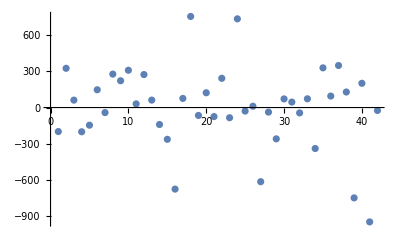

0.859577

```mathematica
lm = LinearModelFit[Transpose[rowdata],u,u]
Show[ListPlot[Transpose[rowdata]], Plot[lm[x],{x,20,40}, PlotStyle->Orange]]
conf = lm["ParameterConfidenceIntervals",ConfidenceLevel -> 0.95]
perd= lm["SinglePredictionBands", ConfidenceLevel->0.95]
residuals=lm["FitResiduals"];
residualsplot=Transpose@{Transpose[rowdata],residuals};
ListPlot[residuals]
lm["RSquared"]
```